## Solve the Lorenz equations

```mathematica
LORENZ[σ_,β_,ρ_]={x'[t]==σ (y[t]-x[t]),
y'[t]==x[t](ρ-z[t])-y[t],
z'[t]==x[t] y[t]-β z[t]}
```

{x'(t)==σ (y(t)-x(t)),y'(t)==x(t) (ρ-z(t))-y(t),z'(t)==x(t) y(t)-β z(t)}

```mathematica
IC[x0_,y0_,z0_] = {x[0]==x0, y[0]==y0,z[0]==z0}
```

{x(0)==x0,y(0)==y0,z(0)==z0}

```mathematica
tFinal=50
```

50

```mathematica
solveit[ic_,t_]:={x[t],y[t],z[t]}/.NDSolve[{LORENZ[10,8/3,28],ic},{x[t],y[t],z[t]},{t,0,tFinal} ,MaxStepSize->10^-5][[1]];
```

```mathematica
soln1[t_]=solveit[IC[10,10,10],t];
```

```mathematica
soln2[t_]=solveit[IC[10.001,10,10],t];
```

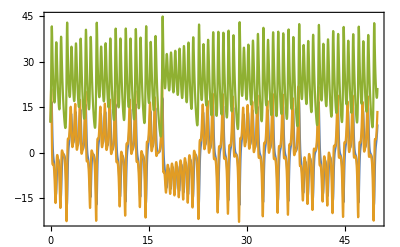

```mathematica
Plot[Evaluate@soln1[t],{t,0,tFinal}]
```

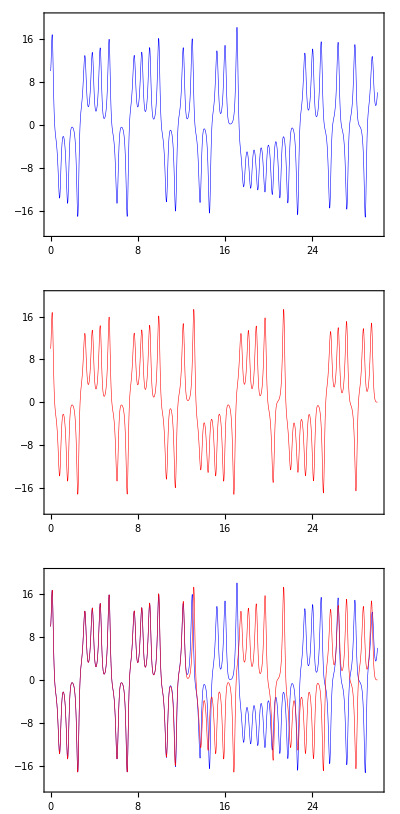

```mathematica
GraphicsColumn[
{
Plot[soln1[t][[1]],{t,0,30},PlotStyle->{Thickness[0.001],Blue},PlotRange->{-20,20}],
Plot[soln2[t][[1]],{t,0,30},PlotStyle->{Thickness[0.001],Red},PlotRange->{-20,20}],
Plot[{soln1[t][[1]],soln2[t][[1]]},{t,0,30},PlotStyle->{{Thickness[0.001],Blue},{Thickness[0.001],Red}},PlotRange->{-20,20}]
}
]
```

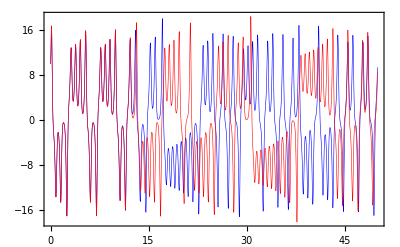

```mathematica
Plot[{soln1[t][[1]],soln2[t][[1]]},{t,0,tFinal},PlotStyle->{{Thickness[0.001],Blue},{Thickness[0.001],Red}}]
```

```mathematica
ParametricPlot3D[{soln1[t],soln2[t]},{t,0,tFinal},PlotPoints->1000,ColorFunction->None,PlotStyle->{Directive[Thickness[0.001],Blue],
Directive[Thickness[0.001],Red]},Boxed->False,Axes->None]
```

-Graphics3D-